```mathematica
ClearAll["Global`*"]
```

## Import spectrum computation from C++ result

Browse the Data folder to find a suitable computation

```mathematica
folders=FileNames[StringJoin[ParentDirectory[NotebookDirectory[]],"/data/examplescenario/decayspec/*"]];
Print[Length[folders]," files found"]
```

300 files found

...and choose one file for testing. We need the primary spectrum as an interpolated function and the decay parameters (masses) to perform the computation.

{{# 20250617_161305},{# primespec:	data/examplescenario/primaryspec/spec_20250617_160430_279/spectr.txt},{# qmax:	4},{# ma:	1.88},{# mb:	0.14},{# mc:	0.14},{# [=>] pabc:	0.929516},{# [=>] Eabc:	0.94},{# B:	1},{# Q:	1},{# epsrel:	1e-05},{# epsabs:	0},{# iter:	100000},{pT,decayspec},{0,453.553}}

primary spec header:
# 20250617_161305 | 
qT | primespec
0 | 12288.3
(...)

decay spec header:
# 20250617_161305 | 
# primespec:	data/examplescenario/primaryspec/spec_20250617_160430_279/spectr.txt | 
# qmax:	4 | 
# ma:	1.88 | 
# mb:	0.14 | 
# mc:	0.14 | 
# [=>] pabc:	0.929516 | 
# [=>] Eabc:	0.94 | 
# B:	1 | 
# Q:	1 | 
# epsrel:	1e-05 | 
# epsabs:	0 | 
# iter:	100000 | 
pT | decayspec
0 | 453.553
(...)

qTmax:
4

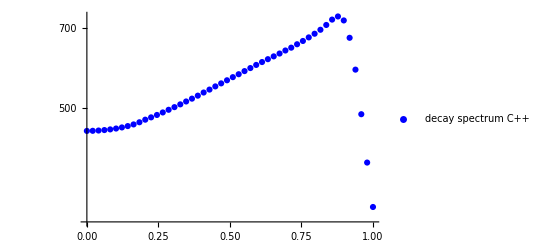

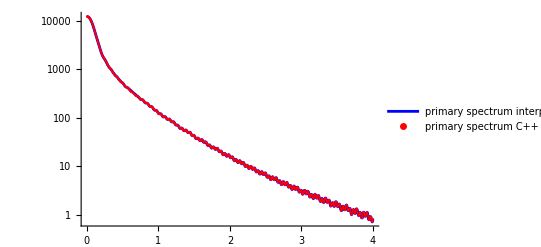

```mathematica
cppspecfolder=folders[[280]];
dataprimespec=Import[StringJoin[cppspecfolder,"/primespec.txt"],"CSV"];
datadecayspec=Import[StringJoin[cppspecfolder,"/decayspec.txt"],"CSV"];

decayspechead=datadecayspec[[1;;15]]
Print["primary spec header:\n",TableForm[dataprimespec[[1;;3]]],"\n(...)"]
Print["decay spec header:\n",TableForm[decayspechead],"\n(...)"]

pTscpp=Transpose[datadecayspec[[15;;]]][[1]];
qTs=Transpose[dataprimespec[[3;;]]][[1]];
qTmax=qTs[[-1]];
Print["qTmax:\n",qTmax]

decayspeccpp=Transpose[datadecayspec[[15;;]]][[2]];
primespeclist=Transpose[dataprimespec[[3;;]]][[2]];

primespecloglist=Log@primespeclist;
primespeclog=Interpolation[Transpose@{qTs,primespecloglist}];
primespec[q_]=Exp[primespeclog[q]];

ListLogPlot[Transpose@{pTscpp,decayspeccpp},PlotLegends->{"decay spectrum C++"},PlotStyle->Blue]
Show[
LogPlot[primespec[qT],{qT,0,qTmax},PlotLegends->{"primary spectrum interpolated"},PlotStyle->Blue],
ListLogPlot[Transpose@{qTs,primespeclist},PlotLegends->{"primary spectrum C++"},PlotMarkers->{Automatic,2},PlotStyle->Red]
]
```

## Small section to derive the analytic expressions relevant for the spectrum computation

```mathematica
Clear[ma,mb,mc,Eabc,B,Q]

w[p_,m_]=√(p^2+m^2);
ustar[t_,v_]=(ma*Eabc+t*v*Q*p)/(w[t*Q,ma]*w[p,mb]);
myassumptions={Element[ma,Reals],ma>0,Element[Eabc,Reals],Eabc>0,Element[Q,Reals],Q>0}

s=Solve[1==ustar[t,v],v];
v1[t_,p_]=v/.s[[1]]//FullSimplify;
t1min[p_]=t/.Solve[0==D[v1[t,p],t],t][[2]]//FullSimplify;
vmin[p_]=v1[t1min[p],p]//FullSimplify;
s2=Solve[1==v1[t,p],t]//FullSimplify;
tmin[p_]=t/.s2[[1]]//FullSimplify;
tmax[p_]=t/.s2[[2]]//FullSimplify;
Print["u*(t,p)==1 at v1(t,p)=",v1[t,p]]
Print["Lower Bound of v-integration given by:\tminimum of v1(t,p) at t=",t1min[p]," and v1=",vmin[p]//FullSimplify[#,Assumptions->myassumptions]&]
Print["Lower Bound of t-integration given by:\tv1(t,p)=+1 at tmin(p)=",tmin[p]//FullSimplify[#,Assumptions->myassumptions]&]
Print["Upper Bound of t-integration given by:\tv1(t,p)=+1 at tmax(p)=",tmax[p]//FullSimplify[#,Assumptions->myassumptions]&]

Clear[w,ustar,g,s,v1,t1min,vmin,s2,tmin,tmax]
```

{ma∈ℝ,ma>0,Eabc∈ℝ,Eabc>0,Q∈ℝ,Q>0}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

u*(t,p)==1 at v1(t,p)=(-Eabc ma+√(mb^2+p^2) √(ma^2+Q^2 t^2))/(p Q t)

Lower Bound of v-integration given by:	minimum of v1(t,p) at t=(√(ma^2 (-Eabc^2+mb^2+p^2)))/(Eabc Q) and v1=(√(-Eabc^2+mb^2+p^2))/p

Lower Bound of t-integration given by:	v1(t,p)=+1 at tmin(p)=(Eabc ma p-ma √((Eabc-mb) (Eabc+mb) (mb^2+p^2)))/(mb^2 Q)

Upper Bound of t-integration given by:	v1(t,p)=+1 at tmax(p)=(ma (Eabc p+√((Eabc-mb) (Eabc+mb) (mb^2+p^2))))/(mb^2 Q)

## Perform the full decay computation in Mathematica

```mathematica
Install[StringJoin[ParentDirectory@NotebookDirectory[],"/Cuba-4.2.2/Cuhre"]];
ComputeDecaySpec[ps_,ma_,mb_,mc_,B_,Q_,qmax_,primespec_, myMaxPoints_,myPrecisionGoal_]:=Module[{pabc,Eabc,w,absgradg,ustar,area,myintegrand,tlower,tupper,vlower,tmin,tmax,vmin,MyIntegral,result},
pabc=1/(2*ma)√(((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2));
Eabc=√(mb^2+pabc^2);

w[p_,m_]=√(p^2+m^2);
ustar[p_,t_,v_]=(ma*Eabc+t*v*Q*p)/(w[t*Q,ma]*w[p,mb]);
myintegrand[p_,t_,v_]=If[ustar[p,t,v]>1 && Abs[v]<1,
t*primespec[t*Q]*1/(√(ustar[p,t,v]^2-1)*√(1-v^2))*1/(w[p,mb]*w[t*Q,ma]),0];



tlower[p_]=(Eabc* ma* p-ma *√((Eabc-mb) *(Eabc+mb) *(mb^2+p^2)))/(mb^2 *Q);
tupper[p_]=(Eabc* ma* p+ma *√((Eabc-mb) *(Eabc+mb) *(mb^2+p^2)))/(mb^2 *Q);
vlower[p_]=(√(-Eabc^2+mb^2+p^2))/p;
tmin[p_]=If[tlower[p]>0,tlower[p],0];
tmax[p_]=If[tupper[p]<qmax/Q,tupper[p],qmax/Q];
vmin[p_]=If[Eabc^2<=mb^2+p^2,vlower[p],-1];

MyIntegral[p_]:=(ma*B*Q*Q)/(π*pabc)*Cuhre[myintegrand[p,t,v],{t,tmin[p],tmax[p]},{v,vmin[p],1},Verbose->0,
MinPoints->0,
MaxPoints->myMaxPoints,
PrecisionGoal->myPrecisionGoal,
AccuracyGoal->Infinity
][[1]][[1]];
result=Map[MyIntegral,ps];
result
]
```

You need to copy the decay parameters from above manually for each new dataset. Let’s compute on a smaller pT-grid, since this is just a test...

```mathematica
Print["Parameters copied from above:\n",TableForm[decayspechead]]

ma=ToExpression@StringReplace[decayspechead[[4]][[1]],"# ma:\t"->""];
mb=ToExpression@StringReplace[decayspechead[[5]][[1]],"# mb:\t"->""];
mc=ToExpression@StringReplace[decayspechead[[6]][[1]],"# mc:\t"->""];
B=ToExpression@StringReplace[decayspechead[[9]][[1]],"# B:\t"->""];
Q=ToExpression@StringReplace[decayspechead[[10]][[1]],"# Q:\t"->""];
Print[Style["!!! ~~~IMPORTANT~~~\n",Bold],Style["!!! Be sure that the cpp values above and mathematica values below coincide!\n",Bold],Style["!!!",Bold]]
Print["ma=",ma]
Print["mb=",mb]
Print["mc=",mc]
Print["B=",B]
Print["Q=",Q]

pTstest=Array[#&,25,{0.001,1}];
Print["Copmute on p=", pTstest]
```

Parameters copied from above:
# 20250617_161305 | 
# primespec:	data/examplescenario/primaryspec/spec_20250617_160430_279/spectr.txt | 
# qmax:	4 | 
# ma:	1.88 | 
# mb:	0.14 | 
# mc:	0.14 | 
# [=>] pabc:	0.929516 | 
# [=>] Eabc:	0.94 | 
# B:	1 | 
# Q:	1 | 
# epsrel:	1e-05 | 
# epsabs:	0 | 
# iter:	100000 | 
pT | decayspec
0 | 453.553

!!! ~~~IMPORTANT~~~
!!! Be sure that the cpp values above and mathematica values below coincide!
!!!

ma=1.88

mb=0.14

mc=0.14

B=1

Q=1

Copmute on p={0.001,0.042625,0.08425,0.125875,0.1675,0.209125,0.25075,0.292375,0.334,0.375625,0.41725,0.458875,0.5005,0.542125,0.58375,0.625375,0.667,0.708625,0.75025,0.791875,0.8335,0.875125,0.91675,0.958375,1.}

```mathematica
decayspectest=ComputeDecaySpec[pTstest,ma,mb,mc,B,Q,qTmax,primespec,100000,5];
Clear[ma,mb,mc,B,Q]
```

Cuhre::accuracy: Desired accuracy was not reached within 100035 function evaluations on 770 subregions.

General::stop: Further output of Cuhre::accuracy will be suppressed during this calculation.

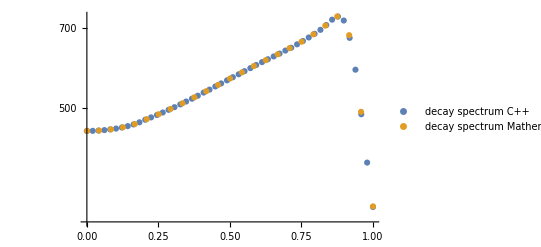

```mathematica
ListLogPlot[{Transpose@{pTscpp,decayspeccpp},Transpose@{pTstest,decayspectest}},PlotLegends->{"decay spectrum C++","decay spectrum Mathematica"}]
```